```mathematica
file1 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\r_0.dat";file2 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\c_0.dat";
file3 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\r_1.dat";file4 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\c_1.dat";
file5= "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\r_2.dat";file6 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\c_2.dat";
file7 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\r_3.dat";file8 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\c_3.dat";
file9 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\r_4.dat";file10= "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\c_4.dat";
file11 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\r_5.dat";file12 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\c_5.dat";
file13 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\r_6.dat";file14= "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\c_6.dat";
file15 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\r_7.dat";file16 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\c_7.dat";
file17 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\r_8.dat";file18= "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\c_8.dat";
file19 = "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\r_9.dat";file20= "G:\\Studia\\IV\\MO\\Laboratoria\\12\\Program12\\Program12\\c_9.dat";
```

```mathematica
res1 = ReadList[file1, {Real, Real}];
res2 = ReadList[file2, {Real, Real}];
res3 = ReadList[file3, {Real, Real}];
res4 = ReadList[file4, {Real, Real}];
res5 = ReadList[file5, {Real, Real}];
res6= ReadList[file6, {Real, Real}];
res7 = ReadList[file7, {Real, Real}];
res8 = ReadList[file8, {Real, Real}];
res9= ReadList[file9, {Real, Real}];
res10 = ReadList[file10, {Real, Real}];
res11 = ReadList[file11, {Real, Real}];
res12 = ReadList[file12, {Real, Real}];
res13 = ReadList[file13, {Real, Real}];
res14 = ReadList[file14, {Real, Real}];
res15= ReadList[file15, {Real, Real}];
res16 = ReadList[file16, {Real, Real}];
res17 = ReadList[file17, {Real, Real}];
res18 = ReadList[file18, {Real, Real}];
res19 = ReadList[file19, {Real, Real}];
res20 = ReadList[file20, {Real, Real}];
```

```mathematica
f[x_]:= x / (1 + 25*(Abs[x])^3);
```

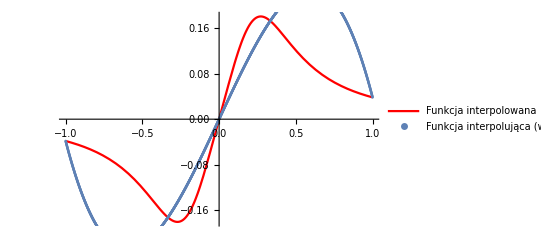

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res1,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły równoodległe) N = 4"}]]
```

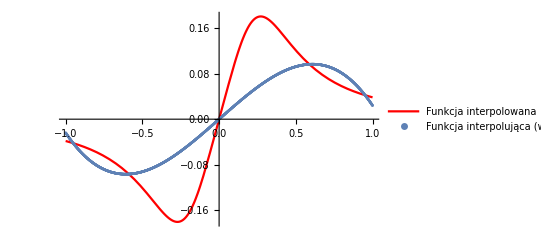

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res2,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły Czebyszewa) N = 4"}]]
```

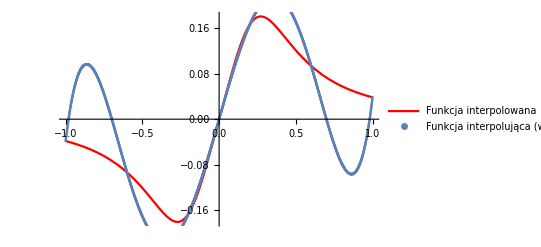

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res3,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły równoodległe) N = 6"}]]
```

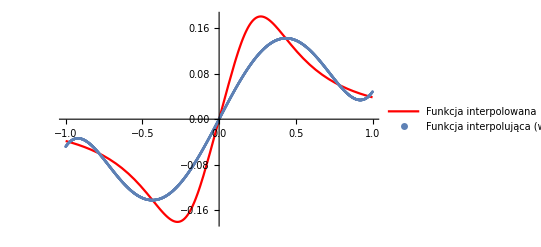

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res4,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły Czebyszewa) N = 6"}]]
```

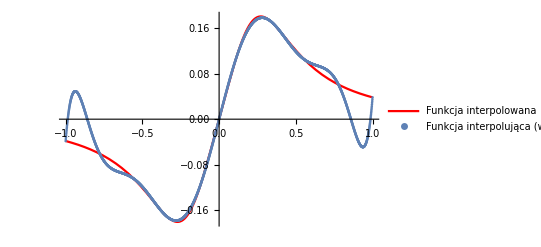

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res5,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły równoodległe) N = 10"}]]
```

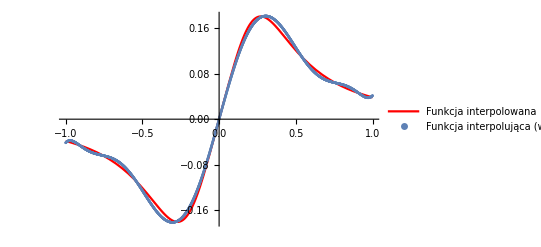

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res6,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły Czebyszewa) N = 10"}]]
```

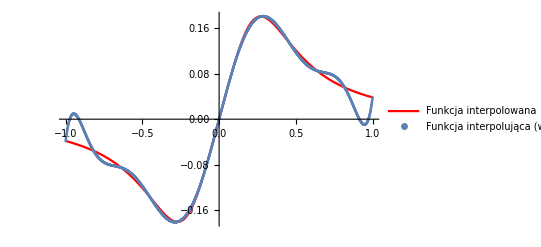

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res7,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły równoodległe) N = 12"}]]
```

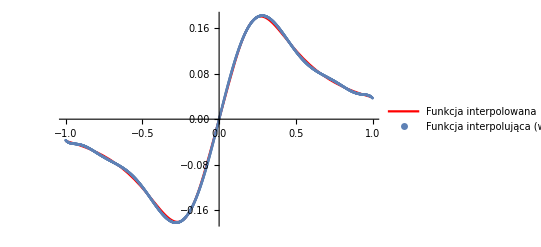

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res8,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły Czebyszewa) N = 12"}]]
```

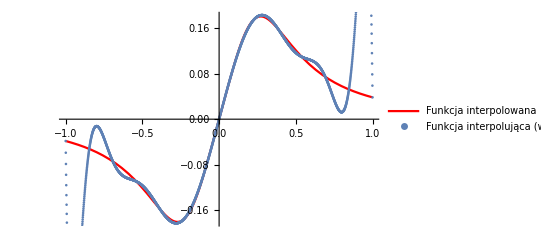

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res9,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły równoodległe) N = 14"}]]
```

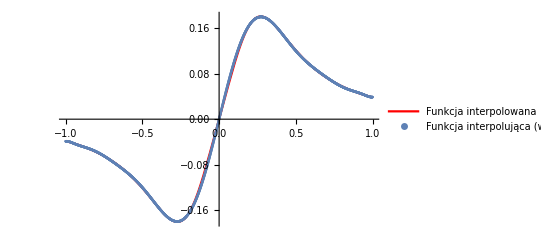

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res10,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły Czebyszewa) N =14"}]]
```

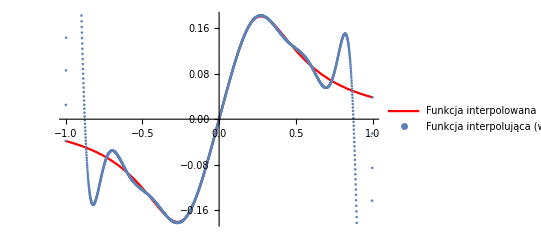

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res11,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły równoodległe) N = 16"}]]
```

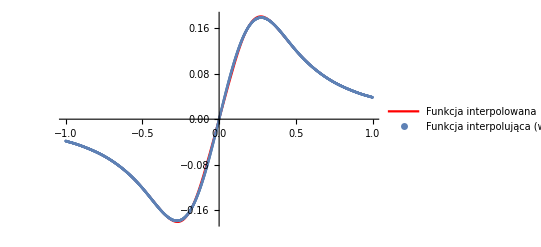

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res12,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły Czebyszewa) N = 16"}]]
```

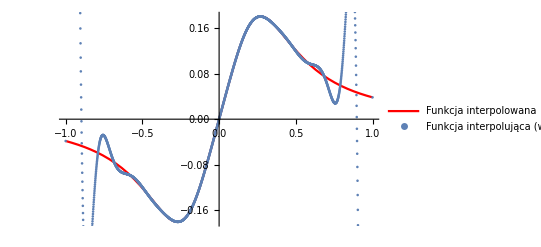

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res13,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły równoodległe) N = 20"}]]
```

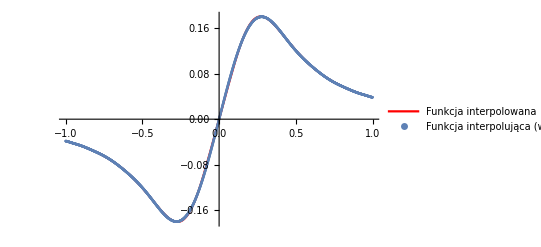

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res14,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły Czebyszewa) N = 20"}]]
```

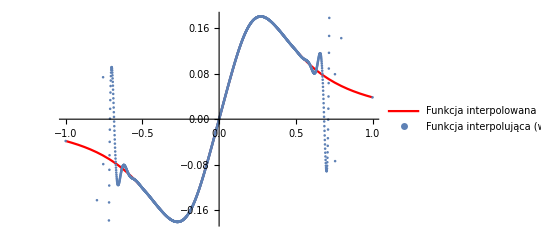

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res15,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły równoodległe) N = 50"}]]
```

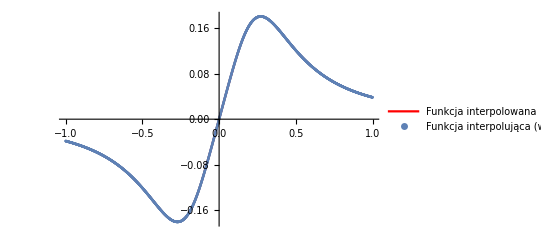

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res16,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły Czebyszewa) N = 50"}]]
```

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res17,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły równoodległe) N = 100"}]]
```

-Graphics-

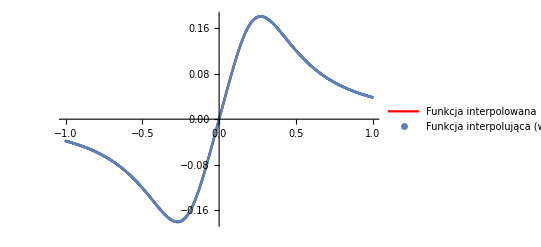

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res18,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły Czebyszewa) N = 100"}]]
```

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res19,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły równoodległe) N = 300"}]]
```

-Graphics-

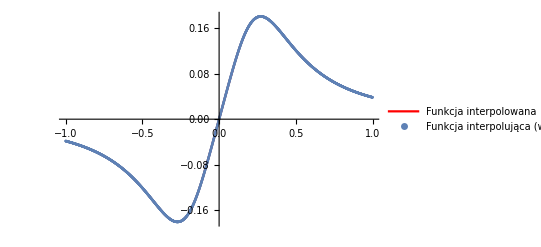

```mathematica
Show[Plot[f[x], {x, -1, 1}, PlotLegends->{"Funkcja interpolowana"}, PlotStyle->{Red}],ListPlot[res20,AxesLabel->{"x", "y"}, PlotLegends->{"Funkcja interpolująca (węzły Czebyszewa) N = 300"}]]
```